```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumAliases[];
```

## Quantum Notation Palette

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Notation`\"]",
"SpanFromLeft",
"SetQuantumAliases[]",
"SpanFromLeft",
"SetQuantumObject[□]",
"SpanFromLeft",
"SetQuantumScalar[□]",
"SpanFromLeft",

"QuantumPartialTrace[□,OverHat[□]]",
"SpanFromLeft",
"QuantumPartialTranspose[□,OverHat[□]]",
"SpanFromLeft",

"QuantumReplace[□,{|□⟩:>|□⟩,|□⟩:>|□⟩}]",
"SpanFromLeft",
"SpanFromLeft",
"SpanFromLeft", 

"DefineOperatorOnKets[□,{|□⟩:>|□⟩,|□⟩:>|□⟩}]",
"SpanFromLeft",
"SpanFromLeft",
"SpanFromLeft", 

"|□⟩","⟨□|","|□_OverHat[□]⟩","⟨□_OverHat[□]|",
"|□_OverHat[□],□_OverHat[□]⟩","⟨□_OverHat[□],□_OverHat[□]|","|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩","⟨□_OverHat[□],□_OverHat[□],□_OverHat[□]|",
"⟨□|□⟩","|□⟩·⟨□|","⟨□_OverHat[□]|·|□_OverHat[□]⟩","|□_OverHat[□]⟩·⟨□_OverHat[□]|",
"⟨□_OverHat[□],□_OverHat[□]|·|□_OverHat[□],□_OverHat[□]⟩","|□_OverHat[□],□_OverHat[□]⟩·⟨□_OverHat[□],□_OverHat[□]|","|□_OverHat[□]⟩·|□_OverHat[□]⟩","⟨□_OverHat[□]|·⟨□_OverHat[□]|",
"OverHat[□]·|□_OverHat[□]⟩","□_OverHat[□]","OverHat[□]","Tr_OverHat[□][□]",
"∑_□^□ □","⊗_□^□□","‖□‖","□/(‖□‖)",
"(□)^†","(□)^*","⟦□,□⟧_-","⟦□,□⟧_+",
"·","⊗","□·□","□⊗□"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,4]],WindowTitle->"Quantum Notation"]
```

NotebookObject[ | Quantum Notation]

## Quantum Algebra Palette

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Notation`\"]",
"SpanFromLeft",
"SetQuantumObject[□]",
"SetQuantumObject[□,□,□]",
"DefineOperatorOnKets[□,{|□⟩:>|□⟩,|□⟩:>|□⟩}]",
"SpanFromLeft",
"CollectFromLeft[□]",
"CollectFromRight[□]",
"Expand[□]",
"CommutatorExpand[□]",
"CommutatorExpand[□,Anticommutators→True]",
"SpanFromLeft",
"CommutatorExpand[□,ReverseOrdering→True]",
"SpanFromLeft",
"CommutatorExpand[□,NestedCommutators→True]",
"SpanFromLeft",
"EvaluateCommutators[□]",
"EvaluateAllCommutators[□]",
"FactorKet[□]",
"CollectKet[□]",
"FactorKetList[□]",
"Simplify[□]",
"⟦□,□⟧_-",
"⟦□,□⟧_+",
"⟦□,□⟧_-=□",
"⟦□,□⟧_+=□",
"□·□=□",
"□^□=□",
"·",
"⊗"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum Algebra"]
```

NotebookObject[ | Quantum Algebra]

## Quantum to Matrix Palette

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Notation`\"]",
"SpanFromLeft",

"MatrixToDirac[(□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □),{4}]", 
"MatrixToDirac[(□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □),{2,2}]",

"TensorToDirac[(□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □)]",
"TensorToDirac[((□ | □
□ | □) | (□ | □
□ | □)
(□ | □
□ | □) | (□ | □
□ | □))]",

"VectorToDirac[{□,□,□,□},{4}]",

"VectorToDirac[{□,□,□,□},{2,2}]",

"MatrixToDirac[(□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □),{2,2},{0_OverHat[1]→a1_(â),1_OverHat[1]→a2_(â),0_OverHat[2]→b1_(b̂),1_OverHat[2]→b2_(b̂)}]",
"SpanFromLeft",


"TensorToDirac[((□ | □
□ | □) | (□ | □
□ | □)
(□ | □
□ | □) | (□ | □
□ | □)),{0_OverHat[1]→a1_(â),1_OverHat[1]→a2_(â),0_OverHat[2]→b1_(b̂),1_OverHat[2]→b2_(b̂)}]",
"SpanFromLeft",


"MatrixToDirac[□,{□}]",
"TensorToDirac[□]",

"DiracToMatrix[□,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]",
"DiracToTensor[□,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]",


"MatrixForm[DiracToMatrix[□,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]]",
"MatrixForm[DiracToTensor[□,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]]",

"DiracEigensystem[□,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]",
"DiracToVector[□|□_OverHat[□],□_OverHat[□]⟩+□|□_OverHat[□],□_OverHat[□]⟩,{{□_OverHat[□],□_OverHat[□]},{□_OverHat[□],□_OverHat[□]}}]"

}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum to Matrix"]
```

NotebookObject[ | Quantum to Matrix]

## Quantum Tests and Measurements

```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Notation`\"]",
"SpanFromLeft",
"QuantumScalarQ[□]",
"KetQ[□]",
"QuantumMeasurement[□|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩+□|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩,{OverHat[□],OverHat[□]}]",
"SpanFromLeft",
"QuantumMeasurement[□,{□},Assumptions→And[□≠□,□≠□]]",
"SpanFromLeft",
"QuantumMeasurement[□,{□},FactorKet→False]",
"SpanFromLeft",
"QuantumDensityOperator[QuantumMeasurement[□,{□}]]",
"SpanFromLeft",
"Part[QuantumMeasurement[□,{□}],1]",
"SpanFromLeft"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum Tests and Measurements"]
```

NotebookObject[ | Quantum Tests and Measurements]

## Quantum Computing Commands

```mathematica
Needs["Quantum`Computing`"];
```

```mathematica
Names["Quantum`Computing`*"]
```

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Computing`\"]",
"SetComputingAliases[]",
"QuantumEvaluate[□]",
"QuantumTable[□]",
"PauliExpand[□]",
"QuantumTableForm[□]",
"FactorKet[□]",
"TraditionalForm[QuantumTableForm[□]]",
"QuantumMatrixForm[□]",
"QuantumTensorForm[□]",
"QuantumMatrix[□]",
"QuantumTensor[□]",
"MatrixQuantum[□]",
"TensorQuantum[□]",
"QubitToDec[|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩]",
"DecToQubit[□,□]",
"QuantumPartialTrace[□,OverHat[□]]",
"QuantumPartialTranspose[□,OverHat[□]]",
"QuantumPlot[□]",
"SetQuantumGate[□,□]",
"QuantumPlot3D[□]",
"SetQuantumGate[□,{□,□}]",
"SetQuantumGate[□,□,Function[{□,□},□]]",
"SpanFromLeft",
"QuantumPlot[QubitMeasurement[□,{OverHat[□],OverHat[□]}]]",
"SpanFromLeft",
"QuantumEvaluate[QubitMeasurement[□,{OverHat[□],OverHat[□]}]]",
"SpanFromLeft",
"QuantumEvaluate[QubitMeasurement[□,{OverHat[□],OverHat[□]},FactorKet→False]]",
"SpanFromLeft",
"QuantumDensityOperator[QubitMeasurement[□,{OverHat[□],OverHat[□]}]]",
"SpanFromLeft"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum Computing Commands"]
```

NotebookObject[ | Quantum Computing Commands]

```mathematica
QubitToDec[|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]]⟩]
```

5

```mathematica
DecToQubit[9,5]
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4],1_OverHat[5]⟩

```mathematica
Needs["Quantum`Computing`"]
```

Welcome to Quantum`Computing`
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

```mathematica
TraditionalForm[QuantumTableForm[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]]
```

|   Input |   Output
0 | |00⟩ | 1/2 |00⟩+1/2 |01⟩+1/2 |10⟩+1/2 |11⟩
1 | |01⟩ | 1/2 |00⟩-1/2 |01⟩+1/2 |10⟩-1/2 |11⟩
2 | |10⟩ | 1/2 |00⟩+1/2 |01⟩-1/2 |10⟩-1/2 |11⟩
3 | |11⟩ | 1/2 |00⟩-1/2 |01⟩-1/2 |10⟩+1/2 |11⟩

```mathematica
QuantumTable[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]
```

{{|0_OverHat[1],0_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩},{|0_OverHat[1],1_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩},{|1_OverHat[1],0_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩},{|1_OverHat[1],1_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩}}

```mathematica
QuantumTableForm[Subscript[ℋ, OverHat[1]]⊗Subscript[ℋ, OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩

```mathematica
FactorKet[1/2 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+1/2 |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+1/2 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+1/2 |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩]
```

Hold[(|0_OverHat[1]⟩+|1_OverHat[1]⟩)⊗(1/2 (|0_OverHat[2]⟩+|1_OverHat[2]⟩))]

```mathematica
(|Subscript[0, OverHat[1]]⟩+|Subscript[1, OverHat[1]]⟩)⊗(1/2 (|Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[2]]⟩))
```

1/2 (|0_OverHat[1],0_OverHat[2]⟩+|0_OverHat[1],1_OverHat[2]⟩)+1/2 (|1_OverHat[1],0_OverHat[2]⟩+|1_OverHat[1],1_OverHat[2]⟩)

```mathematica
QuantumEvaluate[QubitMeasurement[Subscript[ℋ, {OverHat[1],OverHat[2]}],{OverHat[2]}]]
```

QuantumMeasurement::nonket: The first argument … is not a linear combination of kets.

$Aborted

```mathematica
QuantumEvaluate[QubitMeasurement[Subscript[ℋ, {OverHat[1],OverHat[2]}]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩,{OverHat[2]}]]
```

Probability | Measurement | State
1/2 | {{0_OverHat[2]}} | (|0_OverHat[1]⟩+|1_OverHat[1]⟩)⊗(|0_OverHat[2]⟩)/(√2)
1/2 | {{1_OverHat[2]}} | (|0_OverHat[1]⟩+|1_OverHat[1]⟩)⊗(|1_OverHat[2]⟩)/(√2)
Probability | Measurement | State

```mathematica
QuantumEvaluate[QubitMeasurement[Subscript[ℋ, {OverHat[1],OverHat[2]}]·|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩,{OverHat[2]},FactorKet->False]]
```

Probability | Measurement | State
1/2 | {{0_OverHat[2]}} | (|0_OverHat[1],0_OverHat[2]⟩+|1_OverHat[1],0_OverHat[2]⟩)/(√2)
1/2 | {{1_OverHat[2]}} | (|0_OverHat[1],1_OverHat[2]⟩+|1_OverHat[1],1_OverHat[2]⟩)/(√2)
Probability | Measurement | State

```mathematica
?FactorKet
```

FactorKet[expr] factors tensor products of kets in expr. Its output is returned inside a Hold command

```mathematica
?SetQuantumGate
```

After evaluating SetQuantumGate[symbol,narg] symbol will be treated as quantum gate of narg arguments (qubits) by QuantumEvaluate[] and other functions
SetQuantumGate[symbol,narg,Function[{q1,q2...},diracexpr]] replaces symbol with diracexpr (evaluated in q1,q2...) when symbol is part of the argument of QuantumEvaluate.
SetQuantumGate[symbol,{n1,n2}] and SetQuantumGate[symbol,{n1,n2},Function[{q1,q2...},diracexpr]] define symbol as a quantum gate with a number of arguments n1<=narg<=n2

```mathematica
QuantumTable[Subscript[ℋ, OverHat[1]]·Subscript[ℋ, OverHat[2]]]
```

{{|0_OverHat[1],0_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩},{|0_OverHat[1],1_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩},{|1_OverHat[1],0_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩},{|1_OverHat[1],1_OverHat[2]⟩,1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩}}

```mathematica
QuantumTableForm[Subscript[ℋ, OverHat[1]]·Subscript[ℋ, OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩+1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩+1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩-1/2 |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | 1/2 |0_OverHat[1],0_OverHat[2]⟩-1/2 |0_OverHat[1],1_OverHat[2]⟩-1/2 |1_OverHat[1],0_OverHat[2]⟩+1/2 |1_OverHat[1],1_OverHat[2]⟩

## Quantum Computing Gates

```mathematica
Needs["Quantum`Computing`"];
```

```mathematica
SetComputingAliases[]
```

ALIASES:
[ESC]on[ESC]        Quantum concatenation symbol (operator application, inner product and outer product)
[ESC]qket0[ESC]     Ket of qubit 0 template
[ESC]qbra0[ESC]     Bra of qubit 0 template
[ESC]qket1[ESC]     Ket of qubit 1 template
[ESC]qbra1[ESC]     Bra of qubit 1 template
[ESC]qket[ESC]      Ket of qubit template
[ESC]qqket[ESC]     Ket of two qubits template
[ESC]qqqket[ESC]    Ket of three qubits template
[ESC]qbra[ESC]      Bra of qubit template
[ESC]qqbra[ESC]     Bra of two qubits template
[ESC]qqqbra[ESC]    Bra of three qubits template
[ESC]toqb[ESC]      Base-10 Integer to binary qubit template
[ESC]ket[ESC]       Ket template
[ESC]bra[ESC]       Bra template
[ESC]qb[ESC]        Qubit template
[ESC]qv[ESC]        Qubit-value template
[ESC]qketbra[ESC]   Element of a one-qubit operator template
[ESC]qqketbra[ESC]  Element of a two-qubits operator template
[ESC]qqqketbra[ESC] Element of a three-qubits operator template
[ESC]k+[ESC]        Plus ket (eigenstate of the first Pauli matrix)
[ESC]b+[ESC]        Plus bra
[ESC]k-[ESC]        Minus ket (eigenstate of the first Pauli matrix)
[ESC]b-[ESC]        Minus bra
[ESC]k00[ESC]       Ket of Bell State 00
[ESC]k01[ESC]       Ket of Bell State 01
[ESC]k10[ESC]       Ket of Bell State 10
[ESC]k11[ESC]       Ket of Bell State 11
[ESC]b00[ESC]       Bra of Bell State 00
[ESC]b01[ESC]       Bra of Bell State 01
[ESC]b10[ESC]       Bra of Bell State 10
[ESC]b11[ESC]       Bra of Bell State 11
[ESC]kphi+[ESC]     Ket of Bell State phi+
[ESC]kpsi+[ESC]     Ket of Bell State psi+
[ESC]kphi-[ESC]     Ket of Bell State phi-
[ESC]kpsi-[ESC]     Ket of Bell State psi-
[ESC]bphi+[ESC]     Bra of Bell State phi+
[ESC]bpsi+[ESC]     Bra of Bell State psi+
[ESC]bphi-[ESC]     Bra of Bell State phi-
[ESC]bpsi-[ESC]     Bra of Bell State psi-
[ESC]her[ESC]       Hermitian conjugate template
[ESC]con[ESC]       Complex conjugate template
[ESC]norm[ESC]      Quantum norm template
[ESC]trace[ESC]     Partial trace template
[ESC]tp[ESC]        Tensor-product symbol
[ESC]tprod[ESC]     Tensor-product template
[ESC]tprodqb[ESC]   Tensor-product of Qubit template
[ESC]tpow[ESC]      Tensor-power template
[ESC]tpowqb[ESC]    Tensor-power of Qubit template
[ESC]s0[ESC]        0th-Pauli operator (Identity) template
[ESC]s1[ESC]        1st-Pauli operator (X) template
[ESC]s2[ESC]        2nd-Pauli operator (Y) template
[ESC]s3[ESC]        3rd-Pauli operator (Z) template
[ESC]so[ESC]        0th-Pauli operator (Identity) template
[ESC]sx[ESC]        1st-Pauli operator (X) template
[ESC]sy[ESC]        2nd-Pauli operator (Y) template
[ESC]sz[ESC]        3rd-Pauli operator (Z) template
[ESC]sp[ESC]        General Pauli operator template
[ESC]ig[ESC]        Identity gate template
[ESC]xg[ESC]        Pauli-X gate
[ESC]yg[ESC]        Pauli-Y gate
[ESC]zg[ESC]        Pauli-Z gate
[ESC]hg[ESC]        Haddamard gate
[ESC]pg[ESC]        Parametric phase gate
[ESC]sg[ESC]        S Phase gate
[ESC]tg[ESC]        T π/8 gate 
[ESC]swap[ESC]      Swap gate
[ESC]cgate[ESC]     Controlled-Gate template
[ESC]ccgate[ESC]    Controlled-controlled-Gate template
[ESC]cccgate[ESC]   Controlled-controlled-controlled-Gate template
[ESC]cnot[ESC]      Controlled-Not template
[ESC]ccnot[ESC]     Controlled-controlled-Not template
[ESC]cccnot[ESC]    Controlled-controlled-controlled-Not template
[ESC]toff[ESC]      Toffoli gate
[ESC]fred[ESC]      Fredkin gate
[ESC]qg[ESC]        Quantum gate of one argument 
[ESC]qqg[ESC]       Quantum gate of one argument applied to two qubits
[ESC]qqqg[ESC]      Quantum gate of one argument applied to three qubits
[ESC]qgg[ESC]       Quantum gate of two arguments 
[ESC]qggg[ESC]      Quantum gate of three arguments 
[ESC]pqg[ESC]       Parametric quantum gate of one argument 
[ESC]qr[ESC]        Quantum register template 
[ESC]qrg[ESC]       Quantum-register gate template 

SetComputingAliases[] must be executed again in each new notebook that is created, only one time per notebook.

```mathematica
Names["Quantum`Computing`*"]
```

{DecToQubit,MatrixQuantum,PauliExpand,PauliIdentities,QuantumBackground,QuantumConnectionStyle,QuantumControlStyle,QuantumEigensystem,QuantumEigensystemForm,QuantumGatePowers,QuantumGateShifting,QuantumGateStyle,QuantumMatrix,QuantumMatrixForm,QuantumMeter,QuantumMeterStyle,QuantumNotStyle,QuantumPlot,QuantumPlot3D,QuantumSparseArray,QuantumSwapStyle,QuantumTable,QuantumTableForm,QuantumTensor,QuantumTensorForm,QuantumTextStyle,QuantumVerticalTextStyle,QuantumWireStyle,QubitLabels,QubitList,QubitMeasurement,QubitToDec,SetComputingAliases,SetQuantumGate,TensorQuantum,zz020CeroOneQ,zz020Controlled,zz020MultiQubit,zz020TensorPower,zz020TP,zz020TPdat,zz020TPend,zz020TPini,zz020TwoScalarsListQ,zz050Bell,zz050Superpos,𝒞,ℱℛℰ𝒟𝒦ℐ𝒩,ℋ,ℐ,𝒩𝒪𝒯,𝒫,𝒬ℱ𝒯,ℛℯℊ𝒾𝓈𝓉ℯ𝓇,𝓈,𝒮,𝒮𝒲𝒜𝒫,𝒯,𝒯𝒪ℱℱ𝒪ℒℐ,𝒳,𝒴,𝒵,σ,Φ,Ψ,11,10,0,01,00}

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Computing`\"]",
"SpanFromLeft",
"SpanFromLeft",
"SpanFromLeft",

"ℐ_OverHat[□]",
"𝒳_OverHat[□]",
"𝒴_OverHat[□]",
"𝒵_OverHat[□]",

"σ_(0, OverscriptBox[□, ^])",
"σ_(𝒳, OverscriptBox[□, ^])",
"σ_(𝒴, OverscriptBox[□, ^])",
"σ_(𝒵, OverscriptBox[□, ^])",

"ℋ_OverHat[□]",
"𝒮_OverHat[□]",
"𝒯_OverHat[□]",
"𝒮𝒲𝒜𝒫_OverHat[□]",

"𝒬ℱ𝒯_OverHat[□]",
"𝒬ℱ𝒯_OverHat[□]",
"𝒬ℱ𝒯_OverHat[□]",
"𝒬ℱ𝒯_OverHat[□]",

"□_OverHat[□]",
"□_OverHat[□]",
"□_OverHat[□]",
"□_OverHat[□]",

"□_{OverscriptBox[□, ^], OverscriptBox[□, ^]}",
"□_{OverscriptBox[□, ^], OverscriptBox[□, ^], OverscriptBox[□, ^]}",
"𝒞^{OverHat[□]}[□]",
"𝒞^{OverHat[□],OverHat[□]}[□]",

"𝒞^{OverHat[□]}[𝒩𝒪𝒯_OverHat[□]]",
"𝒯𝒪ℱℱ𝒪ℒℐ_OverHat[□]",
"ℱℛℰ𝒟𝒦ℐ𝒩_OverHat[□]",
"𝒫_OverHat[□][□]",

"·",
"⊗",
"ℛℯℊ𝒾𝓈𝓉ℯ𝓇[□,□,□,□]",
"(□)^†"

}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,4]],WindowTitle->"Quantum Computing Gates"]
```

NotebookObject[ | Quantum Computing Gates]

```mathematica
QuantumEvaluate[ℛℯℊ𝒾𝓈𝓉ℯ𝓇[3,30,5,w]]
```

{OverHat[w3],OverHat[w8],OverHat[w13],OverHat[w18],OverHat[w23],OverHat[w28]}

```mathematica
Subscript[ℋ, OverHat[ℛℯℊ𝒾𝓈𝓉ℯ𝓇[3,30,5,w]]]
```

ℋ_ℛℯℊ𝒾𝓈𝓉ℯ𝓇[3,30,5,w]

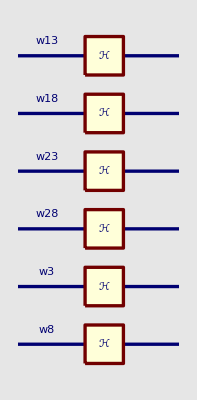

```mathematica
QuantumPlot[%]
```

## Quantum Computing Kets

```mathematica
Needs["Quantum`Computing`"];
```

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Computing`\"]",
"SpanFromLeft",
"SpanFromLeft",
"SpanFromLeft",

"|0_OverHat[□]⟩",
"|1_OverHat[□]⟩",
"⟨0_OverHat[□]|",
"⟨1_OverHat[□]|",

"|+_OverHat[□]⟩",
"|-_OverHat[□]⟩",
"⟨+_OverHat[□]|",
"⟨-_OverHat[□]|",

"|Φ_(OverHat[□],OverHat[□])^+⟩",
"|Ψ_(OverHat[□],OverHat[□])^+⟩",
"|Φ_(OverHat[□],OverHat[□])^-⟩",
"|Ψ_(OverHat[□],OverHat[□])^-⟩",

"⟨Φ_(OverHat[□],OverHat[□])^+|",
"⟨Ψ_(OverHat[□],OverHat[□])^+|",
"⟨Φ_(OverHat[□],OverHat[□])^-|",
"⟨Ψ_(OverHat[□],OverHat[□])^-|",

"|ℬ_(00,OverHat[□],OverHat[□])⟩",
"|ℬ_(01,OverHat[□],OverHat[□])⟩",
"|ℬ_(10,OverHat[□],OverHat[□])⟩",
"|ℬ_(11,OverHat[□],OverHat[□])⟩",

"⟨ℬ_(00,OverHat[□],OverHat[□])|",
"⟨ℬ_(01,OverHat[□],OverHat[□])|",
"⟨ℬ_(10,OverHat[□],OverHat[□])|",
"⟨ℬ_(11,OverHat[□],OverHat[□])|",

"⊗_(n=□)^□|□_(n̂)⟩",
"⊗_(□=□)^□□",
"(|□_OverHat[□]⟩)^(⊗□)",
"(□)^(⊗□)",

"(|□⟩)_□",
"(⟨□|)_□",
"(|□⟩)_{OverHat[□],OverHat[□]}",
"(|□⟩)_{OverHat[□],OverHat[□],OverHat[□]}",

"|□_OverHat[□]⟩",
"|□_OverHat[□],□_OverHat[□]⟩",
"|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩",
"|□⟩",

"⟨□_OverHat[□]|",
"⟨□_OverHat[□],□_OverHat[□]|",
"⟨□_OverHat[□],□_OverHat[□],□_OverHat[□]|",
"⟨□|",

"|□_OverHat[□]⟩·⟨□_OverHat[□]|",
"|□_OverHat[□],□_OverHat[□]⟩·⟨□_OverHat[□],□_OverHat[□]|",
"|□_OverHat[□],□_OverHat[□],□_OverHat[□]⟩·⟨□_OverHat[□],□_OverHat[□],□_OverHat[□]|",
"SpanFromLeft",

"Tr_OverHat[□][□]",
"‖□‖",
"(□)^†",
"(□)^*",

"·",
"⊗",
"□_OverHat[□]",
"OverHat[□]"

}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,4]],WindowTitle->"Quantum Computing Kets"]
```

## Machote de paleta Quantum Computing

```mathematica
Needs["Quantum`Computing`"];
```

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Computing`\"]",
"SpanFromLeft"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum Computing"]
```

## Machote de Paleta Notation

```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
buttonList=Map[Button[#,NotebookWrite[InputNotebook[],#],Appearance->"Palette"]&,
{"Needs[\"Quantum`Notation`\"]",
"SpanFromLeft"
}] /. HoldPattern[Button["SpanFromLeft",___]]:>SpanFromLeft;
CreatePalette[Grid[Partition[buttonList,2]],WindowTitle->"Quantum"]
```